```mathematica
NotebookOpen[CloudObject["https://www.wolframcloud.com/obj/hovestadt/Published/METEORA%20BOOKS/METEORA%20CODE/pages/0000.nb"]]
```

dtg35_shm17FrontEndObject[LinkObject["dtg35_shm", 3, 1]]170000.nbCloudObject[https://www.wolframcloud.com/obj/hovestadt/Published/METEORA%20BOOKS/METEORA%20CODE/pages/0000.nb]

```mathematica
?"Meteora*"
```

```mathematica
ResourceFunction["SaveReadableNotebook"]
```

[◼] | SaveReadableNotebook

```mathematica
SetOptions[EvaluationNotebook[],ShowGroupOpener->False]
```

```mathematica
urlBase="https://www.homegate.ch/rent/apartment/matching-list";
pn=1;
urlPage=urlBase<>"?ep="<>ToString@pn
```

https://www.homegate.ch/rent/apartment/matching-list?ep=1

```mathematica
URL@urlPage
```

URL[https://www.homegate.ch/rent/apartment/matching-list?ep=1]

```mathematica
EmbeddedHTML@URL@urlPage
```

NullURL[https://www.homegate.ch/rent/apartment/matching-list?ep=1]https://www.homegate.ch/rent/apartment/matching-list?ep=1

### Web Page as Text

```mathematica
htmlPage=Import[urlPage, "Text"];
```

```mathematica
StringCases[htmlPage,Shortest["<p><span>"~~a__~~"</span></p>"]:>a]
```

{Rue des Iles 41 H, 1994 Aproz (Nendaz),Rue des Iles 41 H, 1994 Aproz (Nendaz),Rue des Iles 41 H, 1994 Aproz (Nendaz),Bahnhofstrasse 33, 5400 Baden,Ch. de Bellevue 8, 1803 Chardonne,6274 Eschenbach LU,Eichfeldstrasse 25, 8645 Jona,Schaffhauserstrasse 127, 8302 Kloten,Schaffhauserstrasse 127, 8302 Kloten,Schweighofplatz 3, 6010 Kriens,Schweighofweg 16, 6010 Kriens,Schweighofweg 6, 6010 Kriens,Ringstrasse 37, 6010 Kriens,Am Mattenhof 4a, 6010 Kriens,Schweighofweg 6, 6010 Kriens,Sihltalstrasse 101, 8135 Langnau am Albis,Langensandstrasse 25, 6005 Luzern,Langensandstrasse 25, 6005 Luzern,Langensandstrasse 25, 6005 Luzern,Langensandstrasse 25, 6005 Luzern}

### Web Page as XML

```mathematica
xmlPage=Import[urlPage,"XMLObject"];
```

```mathematica
Cases[xmlPage,XMLElement["a",{_,"class"->_,"href"->a_,"data-test"->_},__]:>StringDelete[a,"/rent/"],All]
```

{3000752176,3000752178,3000741113,3000550113,3000576985,3000663095,3000756572,3000718973,3000718975,3000771595,3000690027,3000508704,3000608832,3000736967,3000510915,3000771228,3000503663,3000503661,3000503658,3000516854}

```mathematica
Dynamic@$status
```

```mathematica
projects=Flatten[Function[pn,$status=pn;
urlPage=urlBase<>"?ep="<>ToString@pn;
xmlPage=Import[urlPage,"XMLObject"];
Cases[xmlPage,XMLElement["a",{_,"class"->_,"href"->a_,"data-test"->_},__]:>StringDelete[a,"/rent/"],All]]/@Range[1,50]]
```

{3000752176,3000752178,3000741113,3000550113,3000576985,3000663095,3000756572,3000718973,3000718975,3000771595,3000690027,3000508704,3000608832,3000736967,3000510915,3000771228,3000503663,3000503661,3000503658,3000516854,3000722107,3000649737,3000649740,3000722105,3000649738,109886608,3000751124,3000766184,3000494796,3000675691,3000677135,3000721594,3000752629,3000742401,3000752625,3000763137,3000764086,3000741900,3000728823,3000524334,3000700454,3000766330,3000755072,3000675681,3000668006,3000772587,3000729284,3000772846,3000733225,3000729290,3000670571,3000572138,3000659032,3000603494,3000732704,3000754913,3000412472,3000766620,3000708611,3000726419,3000706912,3000706944,3000653068,3000662088,3000728719,3000574880,3000739791,3000714457,3000763009,3000757477,3000293162,3000293158,3000293159,3000714854,3000740465,3000619620,3000722136,3000034828,3000034810,3000689630,3000674563,3000750550,3000744117,3000603108,3000656400,3000764044,3000599181,3000569699,3000620874,3000294287,3000735607,3000699777,3000742002,3000548345,3000743652,3000532083,3000763901,3000668540,3000664186,3000687837,3000757251,3000652490,3000756651,3000732781,3000752821,3000772592,3000755145,3000770933,3000755147,3000339019,3000755137,3000694378,3000746201,3000741941,3000595814,3000690316,3000461380,3000684212,3000730787,3000691988,3000706577,3000691991,3000635562,3000767886,3000736063,3000746147,3000740483,3000676992,3000234052,3000656638,3000757474,3000758675,3000754720,3000754530,3000675434,3000768255,3000768553,3000717401,3000674885,3000751623,3000752622,3000706708,3000552609,3000759750,3000579173,3000752692,3000684785,3000773110,3000758820,3000726410,3000741812,3000616002,3000739321,3000511012,3000735568,3000728828,3000745346,3000674516,3000764155,3000619461,3000559611,3000114752,3000697901,3000739663,3000261290,3000601922,3000752830,3000770748,3000770295,3000757457,3000744091,3000472909,3000756982,3000691633,3000756981,3000600620,3000771124,3000756979,3000756976,3000725824,3000742527,3000758813,3000673244,3000427514,3000490993,3000443076,3000759780,3000636288,3000748965,3000452058,3000760666,3000484639,3000719000,3000733194,3000553114,3000759400,3000751223,3000743972,3000753321,3000750499,3000750795,3000750729,3000670171,3000689462,3000692274,3000702155,3000726778,3000716828,3000770728,3000742220,3000596593,3000767753,3000613524,3000594774,3000594420,3000766191,3000702702,3000601274,3000613289,3000601475,3000675007,3000675026,3000631725,3000674999,3000708976,2148033515,3000768934,3000757455,3000715487,3000715468,3000477053,3000625906,3000623868,3000739472,3000673161,3000711858,3000721200,3000525369,3000746722,3000667864,3000743948,3000583879,3000689834,3000610488,3000610489,3000508973,3000086456,3000575303,3000741584,3000714949,3000719244,3000697962,3000757479,3000770096,3000768396,3000556439,3000765515,3000576398,3000756377,3000542450,3000746400,3000758331,3000644023,3000644019,3000679355,3000615624,3000534990,3000615617,3000615634,3000706837,3000767847,3000712474,3000396960,3000750919,3000621026,3000633918,3000714624,3000721399,3000091995,3000341052,3000691364,3000673369,3000722130,3000748960,3000752677,3000684171,3000499864,3000759091,3000663114,3000380208,3000740462,3000757460,3000669684,3000766600,3000538892,3000677535,3000699719,3000765046,3000700148,3000726255,3000708700,3000663084,3000772432,3000770271,3000670632,3000712147,3000552543,3000404390,3000740424,3000698358,3000640688,3000733207,3000772355,3000640727,3000719578,3000772353,3000734790,3000772354,3000758804,3000443322,3000604042,3000544996,3000733198,3000056786,3000618894,3000706718,3000694248,3000707077,3000689508,3000677432,3000709228,3000728012,3000757461,3000684339,3000748962,3000748963,3000692173,3000541653,3000755058,3000728709,3000745353,3000712118,3000754529,3000771214,3000752587,3000755086,3000755144,3000755128,3000339876,3000651909,3000511524,3000651851,3000691739,3000751641,3000740364,3000623607,3000763150,3000763880,3000765180,3000745670,3000751631,3000768278,3000661115,3000552883,3000766453,3000755358,3000688372,3000739694,3000755407,3000706762,3000646570,3000646569,3000694534,3000763157,3000606952,3000613482,3000670145,3000557443,3000682288,3000496650,3000758809,3000550219,3000227158,3000550220,3000624254,108829775,108829776,3000755580,3000660821,3000752425,2148003481,3000706733,3000773676,3000717416,3000756455,3000714960,3000769928,3000453356,3000753644,3000753643,3000543905,3000743613,3000476870,3000701993,3000380306,3000759476,3000694775,3000696604,3000686684,3000752663,3000372092,3000716817,3000633917,3000648023,3000727970,3000727966,3000664174,3000538433,3000663172,3000739882,3000316053,3000453339,3000748508,3000702261,3000772796,3000619361,3000660146,3000712712,3000640058,3000566064,3000692200,3000692203,3000752545,3000659099,3000702147,3000597888,3000734814,3000699701,3000757471,3000574474,3000761125,3000752624,3000757472,3000662050,3000662048,3000662047,3000770713,3000770432,3000741509,3000735652,3000721131,3000721878,3000721879,3000699624,3000755448,3000610172,3000689582,3000293340,3000689583,3000717834,3000419666,3000585074,3000650471,3000661534,3000506461,3000689274,3000604144,3000235357,3000386679,3000756843,3000623176,3000731070,3000306070,3000711935,3000575398,3000761296,3000761320,3000749316,3000711809,3000663273,3000663245,3000663242,3000663238,3000772692,3000719088,3000591573,2148036380,3000757466,3000541720,3000718597,3000580355,3000539784,3000515294,3000416553,3000460416,3000460420,3000619860,3000635587,3000650175,3000612885,3000630810,3000759595,3000673486,3000715221,3000770293,3000756456,3000674754,3000627456,3000636128,3000753632,3000627390,3000655781,3000225729,3000547769,3000695669,3000419108,3000750974,3000630807,3000769486,3000757459,3000479705,3000702006,3000393922,3000702234,3000752654,3000727859,3000752645,3000675294,3000702233,3000771203,3000675563,3000595508,3000709327,3000615602,3000064423,3000757454,3000546002,3000727789,3000478956,3000754611,3000677824,3000520164,3000586911,3000744118,3000747461,3000733456,3000692264,3000666898,3000763456,3000757478,3000739306,3000679368,3000769951,3000465635,3000725408,3000739696,3000662044,3000662066,3000692387,3000508524,3000549609,3000549610,3000706925,3000706907,3000767739,3000730433,3000580350,2147853185,3000676339,3000644598,3000546170,3000685066,3000685065,3000760667,3000615181,3000199711,3000680154,3000606796,3000661512,3000767889,3000673599,3000579221,3000563245,3000609706,3000603939,3000388492,3000758817,3000638930,3000735523,3000729740,3000417992,3000383593,3000656719,3000714111,3000723326,3000750872,3000714646,3000719159,3000722060,3000763149,3000668292,3000261089,3000427953,3000767604,3000692358,3000313689,3000730810,3000770162,3000768890,3000523901,3000745257,3000676104,3000765527,3000631689,3000625512,3000556208,3000137066,3000610750,3000621790,3000638942,3000740641,3000740640,3000740643,3000388495,3000602921,3000234830,3000763195,3000767774,3000621061,3000722181,3000596909,3000691754,3000600617,3000591583,3000526580,3000613176,3000691755,3000741506,3000741508,3000741507,3000527039,3000631246,3000733158,3000407453,3000731644,3000641988,3000588970,3000588972,3000588971,3000659195,3000740111,3000725843,3000691253,3000691267,3000577134,3000630834,3000575477,3000643714,3000495532,3000742001,3000742402,3000742399,3000442174,3000575516,3000506750,3000506748,3000628590,3000741497,3000728096,3000758336,3000728104,3000728042,3000638165,3000603335,3000747894,3000479441,3000495508,3000687692,3000679529,3000679702,3000693589,3000628187,3000563603,3000728617,3000531852,3000574731,3000694824,3000389631,3000763076,3000770289,3000586785,3000694596,3000661533,3000679351,3000739688,3000691671,3000583932,3000614742,3000739428,3000692389,3000706904,3000569945,3000730700,3000719685,3000586806,3000759375,3000746245,3000745455,3000452076,3000758816,3000656635,3000650503,3000643852,3000086439,3000369405,3000716922,3000552861,3000748964,3000752541,3000650543,3000237849,3000720121,3000506647,3000601003,3000633926,3000617883,3000666144,3000571668,3000638680,3000750750,3000493876,3000172084,3000492539,3000712432,3000743616,3000635862,3000635869,3000635871,3000452083,3000672156,3000702827,3000690317,2147836040,3000568468,3000756573,3000691632,3000601150,3000390319,3000756569,3000388475,3000514004,3000756571,3000756570,3000661242,3000617875,3000569676,3000758808,3000599691,3000725454,3000770752,3000754760,3000730371,3000692391,3000688036,3000181598,3000611309,3000765440,3000558026,3000627878,109826071,3000773116,3000647758,3000601459,3000722029,3000595943,3000769930,3000467162,3000570553,105321385,3000544139,3000754651,3000526882,3000656665,109964544,3000479933,3000631117,3000652545,3000666083,3000759754,2147838382,3000765185,3000742114,3000747688,3000740441,3000740436,3000711945,3000754468,3000702647,3000773270,3000773272,3000773284,3000371630,3000302359,3000683954,3000574902,3000631050,3000570073,3000703520,3000602618,3000020485,3000726607,2148024993,2147994348,3000745799,109672993,3000298501,3000760665,3000758481,3000650279,3000583211,3000569245,3000578360,3000759868,3000689418,3000729276,3000064074,3000764136,3000721996,3000768471,3000751414,3000739236,3000770287,3000753023,3000399170,3000767803,3000725599,3000619942,3000730704,3000601940,3000762884,3000754489,3000766391,3000391259,3000570313,3000700594,3000699813,3000758806,3000727931,3000702797,3000759748,3000574340,3000743387,3000576422,3000756451,3000763015,3000574665,3000751684,3000659571,3000637054,3000620164,3000746660,3000746720,3000743459,3000747363,3000560086,3000375897,2147998407,2147998405,3000747853,3000690532,3000323665,3000712309,3000742390,3000730861,3000350296,3000532708,3000640147,3000757463,3000729961,3000759416,3000599876,3000735196,3000742188,3000689925,3000586982,3000700050,3000621799,3000471775,3000753736,3000602536,3000195192,3000401356,3000577312,3000766307,3000746285,3000763375,3000735532,3000772679,3000679367,3000687043,3000669616,3000666787,3000679548,3000721688,3000679577,3000359522,3000585105,3000763079,3000709282,3000691637,3000763851,3000717154,3000712291,3000701891,3000726415,3000549425,3000739652,3000763508,3000739858,3000744122,3000320840,3000750741,3000611680,3000729064,3000751324,3000611980,3000635642,3000562179,3000731133,3000739707,3000741615,3000587004,3000537057,3000554898,3000554899,3000635790,3000691386,3000020834,3000053465,3000318904,3000586588,3000733583,3000606925,3000611702,3000682287,3000755501,3000703518,3000741805,3000336910,3000601632,3000510706,3000656460,3000744199,3000729007,3000763775,3000767789,3000766542,3000766045,3000770415,3000633158,3000712044,3000712103,3000733462,3000605480,3000627634,3000659198,3000756535,3000755578,3000743410,3000235866,3000689258,3000666794,3000633591,3000717085,3000594556,3000697973,3000536401,3000679489,3000544912,3000098501,3000732572,3000676884,3000573244,3000650213,3000733161,3000689436,3000669608,3000757123,3000753324,3000758333,3000529976,3000733661,2148028982,3000673007,3000765095,3000765314,3000751316,3000766358,3000752865,3000759510}

```mathematica
Length@projects
```

1000

### Public to cloud

```mathematica
fn=Export[CloudObject["homegate1000.txt",Permissions->"Public"],Compress@projects,"Text"]
```

CloudObject[https://www.wolframcloud.com/obj/amomorning/homegate1000.txt,Permissions→Public]

```mathematica
SetOptions[fn,Permissions->"Public"]
```

{Permissions→Public}

```mathematica
Compress@projects
```

1:eJxdm02uLclthB8gT6xdeAfJJPNvDx5ZO/DAgEcaSIv2Mhw8rdfni4sGGp1ddasqk2QwguT5j//++3/9z//95devf/zbr1+//vN///HPv/1V/5FjjLNmnO3L+11WROSfy7WGLc9+d/253DvHW3jUXmd+l3HfSV/i5hMLf7vfGPN8XzTuGfW9Ou5NPDn327g5xgt78pwXj0p9py/Dlgs3x77r+94zZ4zvi3ZpQ76s4Tcvv/n+7d+11Pfdu7UJHFXExHv0Sfe7rFfnfU20dbAvsDyR2O7UQRbtueeDPWeN8Kv4252BDZ1d48I1KmQVvOjeiYOclYn36rOX7SgTfytHgmv0ji52tK/+BQPOdfFV800cjq7ews2ZkzvSzW/gRfJZWFuHlV8r7PUG3GqPLJ5kTvrgWfUQCiX70dn33hP71TkGjn1unSWuyp7TlgVnXzk2PlLPvZdWOHjUOnUv3pvvwFVOVC3aV//GZ+iPz/fqfBl72hKR8Vk+PtkCpUZt+H48Ow1FRn5NpmO+CNBeBkx2305asBbC96zGJLxXeHVowRi0rxwaN2uFc17vBZxQMbbfd4N96qew/Zr0yVybwPDewUkq6PQX3yfXzYKLliAHV1NvStroDQuNBYzZ8iNE6L7nMn7l3wt/qxB9jMG9cbXd+xoy3ImlnvTgomsFt3DGy/Sr38/I3sGzq0TNV2kJRyeN9ypOCkZ56wZCQ/Ea3+3XVjTTc2oyrHKcy/fGYxzpeI5fJcbmWpvRfS6BMfegT+o7itYfBYNu5Uyc5MwasL5cdCfzgkKSmHM3c+YS5NCgtSxSVhGQ952LUH/XYjY+zAu7YYQvEhLQvsoahlcHUbZ01VBFaf77VUt4dPxROA2Z7PC9JyO4QWUcwoi8n7Gv8MWjYjPohIQJf1a+HeYbsq+BKhFJkJPF/FsLXicYiWVYVyQU6xH5Q55Bcwue6e35yE3mDkteiiIeuyKUKfXoOy+X07jYMeSvGnBvudEzk4nW8SNjW3TrKlzlg414rzOZ1Vv0JY5OiZ0311yT8HVvMHByAq5ryivJkcZ7SMelaCerfYfIkHsy9ks55ntWteZApjsK7g2QEdtIJj5xIibcDHAGhVgET+NZAlpipsQNZWvaN+mxCqJ6PMlxzL5NdXBWI8BzlENr06BzElXGpAMrrA4BWRR4ml8dC405YX05+3pMXucAZATPazLhim7YsuhI4sCkLpIDg9wsuAU9ed7HqwWcFBIOZmctJ8I540zerGMmN7u/PXaK4yiZrTAUfcTYjjJcDaX6Y0uAjDY/eDhKsCC9wttLRMpXRpiV98jr4tJjlfbgZmsuCSSmpwMY2cplmzGoNwHMb17Er7Z7k8eucLi+BBcdJvhEgUXdkAiUrOj8Ypf4jBD1tihj7DemMB13lsTN0h6P+HwTSwF9MX73okFX8y3m351gBUvqydim80kdViLohLGI7l4GI/SlZQ3xC8SClAeRX1dJa7U0qbWN9cmgpB8tTL436yje5jcrD5DlhodGihPTKPzIFk+IlH4QECmVmy3TifLDggJK+mQrAh7s9Y9sSIITFsFNJ2UOrDAic9uGwOKHk7q7dYo70ia7fps+qTTAsMp7SV0a6ljAeNRlcrNBlSomwGTdKhy40dUOfkYOF7zF4kcjI5mbrMaiyyQXFTcTKfwe3VAoDDuNySi7CVSRr28mTWUngKq+yvy5tCk64VvMKX0zYj8VvsOvGum90N3K7En46k1QW8kdrBoQCGeJukO5FLKgxdGBt0uYTNqo/6ETvkVpqUzGYx+PNSdlTGOb7WbMztoS8fkauPUSMPIm+fOq2MuUl1EXaVTyOvFY4/wzGN2SD6wUfVyHMWhFGL2ICqgVX9kS29fuLsiYVCfZpqg4WYGuXorWlgukPbGL8nAYqsykDO9yFuFayoq1kX4TnV/OYdxsA8xbPcGBxU2CWUNU3DS7Mp0ZxeJItx4TJtvqddL32ELrRXh7SaUOWwJF9Zxlik/bZzFkPwJydNmFuEFFv+SiAArtnoS5JFOW6zIaVPQK0CeuycJRXwXNU0IRJP2rLCrV9QSjtjInWyTxe1iFYvWTPssPUfuUkewcqWEk2flkqV8qOlEEo3Fl2aj1O85CNH3xb+WQ5UuGq/DWSz+sIcrL6ILiCyDTSl05TNIUg6rJNNOPjgeBcbdlMiVUYIrccbC4I8ZPttEkgFXuS1ojlH/8Zi0hlro+RYqfDXWWmz0SLjxSDJf8uM/ZUZL4qyQ4t5WrrGIeLwm4rQ9ofXkoY2wQQ5fuJsQI2Jmbe2nljIUo6oKyaQlPxtKkllDLa1s6V7q3OC4r12WFIeERq95doHFZQvEgvb6GLev6knld58PAGZbnxNqZYBQJgBgRxCCGzrjn+pLg9fyblcpNWtBVOvvCVebLZFW0r1pti6Kl4lHPL/kRlaR4GumUuDb+djXkmq42FapnI/ab4wB/pee2l0IuEXamteEyBsJKgc+l9N5LipZloqXLRtQ/EsfMc48105aOsKBCch6L0El/7uW0ZRqr2wYjj42K9ZSM8ovPuVmr/VAiGEWwwW8WJXgIHP018FmbPwA3ybn5aO7NQme1kbYtmY3EFikA9BqWjJeckJptskjaLN2Klc8amh3ePPY1rbzePuwJyAqOZ5HlHLuam2SrMw6bWDInlaQSO9LinItlo6UcYnxC4Pdwki+sZzkenV/bN+71bL9dGcGjOmlQ8AhTvzfnSyt06jPTk5f1ZM9lI0pXy0o/0yi+HkU0C6K3bmZvSebzFPNyughHQar1vZXID9ufq7wYPc+5PA0BFs+qWDLuahxLA3ME8tG6YsgkxGWcvkxpiAKZ5+iUmdp2l3dgQbv5k0SsIEU20uUMlquE5iDxTVOtRS2Oa4/aTNadgMqW2745EZIykJUUm6k9WzIk+6+XLc1jjymNHOQqH8wZv+FLLpfB2D+b5ES+sHCSbU+ydmUc7qiXLCl2SY5uxq5kdFmBCWgEkaHtwJPUH//oWrEClQvkZJ1HRFo/kF+xTnN/YhSp7ZZ1B68TyPtY3BGoGoG0qQkBP9tjeZMFZfmRVVWix1PwqMxJjx3X5k9qG+t71sAWjzOSn1FMi9Ii4BvyKsavyCb1nrxhGGOk/MtQoJibWdYQ57NGoyzGSq41gwUxkwLvdAEWf7vYTdGG+N4uOME3ur2JkIw85qIx2MPbM1ivafsWOeH4IdE3p2J6SVEjz6Gb6ZiRnpQz043CnocClgloxiDWyZvZzhfGkOdI0ljgDBZYm6uAQHbCofAMo2qfR1HTiRJvX15f4kXzDOJGxvRZFirn+hRwcDWoNHuihHRLjgPM+SynLzkZ8Oxga3hYLWOqT1LDlxy+6mkkZwXkz92yppbMYz08MTU6klgBHWnWsKusPiv7mtLsEhT45KfpY0uKiykGYY3kAtvs4h3pdFf52cK8FnS6mQw5b3AOZkjD8pwP648iRYXAKacf+x7rlAtyrOH3rD0meWDBfoNJU5SRonVec/7ObHAVfSW7GqJ1SLjZxUmWybztqm9iQ+hudve7XPUjW7E40A0Sb42z1fRiUw7fbu8jQsV7rLBQk38rCuHTV7DgEnXhaEsO1uKVNTa2oB1dr8kk5zO6XcLlYlmp28xW3VLSZJF0kzJJeiwy1UraqFtrTMc6WbLr2KTTXawkTnZ92eu8FfZexP5MKS0mzRHkDF3vYcExBr9ZDIm9JalyjsXI/BzG0kdz6K2boda1YjhL0bK+3NLRpicFV+QM3j7pEhzFlEw6fflsyc7TslGt3aOX7PHMy/zbs0p/LD8EMrtzAa+77A1/RmcNY03TCZ6x/ewnW2GBReHOsPDJFTVsinFzIPKzZGkoTO/LZHxUT926A3MM6D1OqTbnp2o7g3MwnRbIvnIk05MCli2929WDr7lvkGxLOiVLUtKKPGclcjqhxOP5DuXOPXgYPX2Ee7vAemmE+sEfqaQl/ouU8JECl7BrE2J7UORfX6EMGEmIUU6wBkhxak/UhDXTRo39u34uA+jILb9wSq8bo2TpP0qXXV6nnn2/+dIf3qt/SFMX1ZCw16Zeuq7tPVfnh8V8GmHwqw0wLmQ8K072TK4vpy2BA/IoDpJm1+c42ZCPgv3UYz7NGDbE1j6Kr8rFIlLrAzQdu7xq4zW/e1SfOtis30X+PljlnmTTsSTL3m97CmDYEJhPypG5d2zqSJG2a0A+D1Ox3MyGXZmp1geeaHzOovQ0EWsMouyAgU/rlyqkwuhSPJ/NKIMfCTpOXCvwf7AJtiCTjQiRQYrsFrvGcRbF7tZXGEEY/vMC+SAfNa81T4pTLj3ZDnDKZsdU1S344CmDw/lCBU64fRCUZyUK5BNQpKWKSA7qKJGZzEork8gMNjooZHDWZjMw5Y4U7B1JKzBjbClFq01adaqfREfq0SP7SINQEU2W3/Zgi1nE6r5v/tTJ1fixdGZtGmVQWKS8ihuMaRmjhYXlItKlVBxxmqgByGYkbPS3j9JKHY/MS65AjfKsS37EfhkpwtRrMchSVrMU4nH/rx96neXGODZFnAdRJvRazK5Pn/F9svaXNsSlHGm/ekhW1KqVFd3M2HG62uu5Q5+PYhmsf/9DtviMtfUQGwshgnJrNJl00FVoUCWBRXZ8F3+18xE01Apv/pyMtXkDji7omFmc658h2UBjXONHPUb8/Yx6xVKl1A/pkoioF1Bt/E/pddLbxYadO5Pgi+KQWc83TA1EcjZDydnGaIUjOLqPn+GrxMRYrpBCpW/E5n574omN4v6hzncpc7Ke2ktj5VaOeuJPyEfTKhA9WofYl9Y18Xf38hkn1oG21491Gqa5e0bCJmQsO8vRrDAfF27Ww3D8zcswvr+6F2jSsAxUK9hklgV9BsaCfVvnQQG7yuJ3+M866JPby1HdOylz72DCzbSR4/7VCxHpcILxU39y9cMyyVo2PFbJsf8urlo1XSZiN1vhznKUwt0idJBqi3lae+RwfrUnOewnEs+GXav4G67xg5vlXDa+u8kolk+2N1ULO8nwnjP5ciOhNeU6mxHb05rqN9nTUD6yjPPnTyH/YKbXfgWgRGh+tey3nrJYOG7YTyQ2S+D9ywUjGMox4/8BUxE9yw==

```mathematica
Uncompress@Import["https://www.wolframcloud.com/obj/amomorning/homegate1000.txt"]
```

{3000752176,3000752178,3000741113,3000550113,3000576985,3000663095,3000756572,3000718973,3000718975,3000771595,3000690027,3000508704,3000608832,3000736967,3000510915,3000771228,3000503663,3000503661,3000503658,3000516854,3000722107,3000649737,3000649740,3000722105,3000649738,109886608,3000751124,3000766184,3000494796,3000675691,3000677135,3000721594,3000752629,3000742401,3000752625,3000763137,3000764086,3000741900,3000728823,3000524334,3000700454,3000766330,3000755072,3000675681,3000668006,3000772587,3000729284,3000772846,3000733225,3000729290,3000670571,3000572138,3000659032,3000603494,3000732704,3000754913,3000412472,3000766620,3000708611,3000726419,3000706912,3000706944,3000653068,3000662088,3000728719,3000574880,3000739791,3000714457,3000763009,3000757477,3000293162,3000293158,3000293159,3000714854,3000740465,3000619620,3000722136,3000034828,3000034810,3000689630,3000674563,3000750550,3000744117,3000603108,3000656400,3000764044,3000599181,3000569699,3000620874,3000294287,3000735607,3000699777,3000742002,3000548345,3000743652,3000532083,3000763901,3000668540,3000664186,3000687837,3000757251,3000652490,3000756651,3000732781,3000752821,3000772592,3000755145,3000770933,3000755147,3000339019,3000755137,3000694378,3000746201,3000741941,3000595814,3000690316,3000461380,3000684212,3000730787,3000691988,3000706577,3000691991,3000635562,3000767886,3000736063,3000746147,3000740483,3000676992,3000234052,3000656638,3000757474,3000758675,3000754720,3000754530,3000675434,3000768255,3000768553,3000717401,3000674885,3000751623,3000752622,3000706708,3000552609,3000759750,3000579173,3000752692,3000684785,3000773110,3000758820,3000726410,3000741812,3000616002,3000739321,3000511012,3000735568,3000728828,3000745346,3000674516,3000764155,3000619461,3000559611,3000114752,3000697901,3000739663,3000261290,3000601922,3000752830,3000770748,3000770295,3000757457,3000744091,3000472909,3000756982,3000691633,3000756981,3000600620,3000771124,3000756979,3000756976,3000725824,3000742527,3000758813,3000673244,3000427514,3000490993,3000443076,3000759780,3000636288,3000748965,3000452058,3000760666,3000484639,3000719000,3000733194,3000553114,3000759400,3000751223,3000743972,3000753321,3000750499,3000750795,3000750729,3000670171,3000689462,3000692274,3000702155,3000726778,3000716828,3000770728,3000742220,3000596593,3000767753,3000613524,3000594774,3000594420,3000766191,3000702702,3000601274,3000613289,3000601475,3000675007,3000675026,3000631725,3000674999,3000708976,2148033515,3000768934,3000757455,3000715487,3000715468,3000477053,3000625906,3000623868,3000739472,3000673161,3000711858,3000721200,3000525369,3000746722,3000667864,3000743948,3000583879,3000689834,3000610488,3000610489,3000508973,3000086456,3000575303,3000741584,3000714949,3000719244,3000697962,3000757479,3000770096,3000768396,3000556439,3000765515,3000576398,3000756377,3000542450,3000746400,3000758331,3000644023,3000644019,3000679355,3000615624,3000534990,3000615617,3000615634,3000706837,3000767847,3000712474,3000396960,3000750919,3000621026,3000633918,3000714624,3000721399,3000091995,3000341052,3000691364,3000673369,3000722130,3000748960,3000752677,3000684171,3000499864,3000759091,3000663114,3000380208,3000740462,3000757460,3000669684,3000766600,3000538892,3000677535,3000699719,3000765046,3000700148,3000726255,3000708700,3000663084,3000772432,3000770271,3000670632,3000712147,3000552543,3000404390,3000740424,3000698358,3000640688,3000733207,3000772355,3000640727,3000719578,3000772353,3000734790,3000772354,3000758804,3000443322,3000604042,3000544996,3000733198,3000056786,3000618894,3000706718,3000694248,3000707077,3000689508,3000677432,3000709228,3000728012,3000757461,3000684339,3000748962,3000748963,3000692173,3000541653,3000755058,3000728709,3000745353,3000712118,3000754529,3000771214,3000752587,3000755086,3000755144,3000755128,3000339876,3000651909,3000511524,3000651851,3000691739,3000751641,3000740364,3000623607,3000763150,3000763880,3000765180,3000745670,3000751631,3000768278,3000661115,3000552883,3000766453,3000755358,3000688372,3000739694,3000755407,3000706762,3000646570,3000646569,3000694534,3000763157,3000606952,3000613482,3000670145,3000557443,3000682288,3000496650,3000758809,3000550219,3000227158,3000550220,3000624254,108829775,108829776,3000755580,3000660821,3000752425,2148003481,3000706733,3000773676,3000717416,3000756455,3000714960,3000769928,3000453356,3000753644,3000753643,3000543905,3000743613,3000476870,3000701993,3000380306,3000759476,3000694775,3000696604,3000686684,3000752663,3000372092,3000716817,3000633917,3000648023,3000727970,3000727966,3000664174,3000538433,3000663172,3000739882,3000316053,3000453339,3000748508,3000702261,3000772796,3000619361,3000660146,3000712712,3000640058,3000566064,3000692200,3000692203,3000752545,3000659099,3000702147,3000597888,3000734814,3000699701,3000757471,3000574474,3000761125,3000752624,3000757472,3000662050,3000662048,3000662047,3000770713,3000770432,3000741509,3000735652,3000721131,3000721878,3000721879,3000699624,3000755448,3000610172,3000689582,3000293340,3000689583,3000717834,3000419666,3000585074,3000650471,3000661534,3000506461,3000689274,3000604144,3000235357,3000386679,3000756843,3000623176,3000731070,3000306070,3000711935,3000575398,3000761296,3000761320,3000749316,3000711809,3000663273,3000663245,3000663242,3000663238,3000772692,3000719088,3000591573,2148036380,3000757466,3000541720,3000718597,3000580355,3000539784,3000515294,3000416553,3000460416,3000460420,3000619860,3000635587,3000650175,3000612885,3000630810,3000759595,3000673486,3000715221,3000770293,3000756456,3000674754,3000627456,3000636128,3000753632,3000627390,3000655781,3000225729,3000547769,3000695669,3000419108,3000750974,3000630807,3000769486,3000757459,3000479705,3000702006,3000393922,3000702234,3000752654,3000727859,3000752645,3000675294,3000702233,3000771203,3000675563,3000595508,3000709327,3000615602,3000064423,3000757454,3000546002,3000727789,3000478956,3000754611,3000677824,3000520164,3000586911,3000744118,3000747461,3000733456,3000692264,3000666898,3000763456,3000757478,3000739306,3000679368,3000769951,3000465635,3000725408,3000739696,3000662044,3000662066,3000692387,3000508524,3000549609,3000549610,3000706925,3000706907,3000767739,3000730433,3000580350,2147853185,3000676339,3000644598,3000546170,3000685066,3000685065,3000760667,3000615181,3000199711,3000680154,3000606796,3000661512,3000767889,3000673599,3000579221,3000563245,3000609706,3000603939,3000388492,3000758817,3000638930,3000735523,3000729740,3000417992,3000383593,3000656719,3000714111,3000723326,3000750872,3000714646,3000719159,3000722060,3000763149,3000668292,3000261089,3000427953,3000767604,3000692358,3000313689,3000730810,3000770162,3000768890,3000523901,3000745257,3000676104,3000765527,3000631689,3000625512,3000556208,3000137066,3000610750,3000621790,3000638942,3000740641,3000740640,3000740643,3000388495,3000602921,3000234830,3000763195,3000767774,3000621061,3000722181,3000596909,3000691754,3000600617,3000591583,3000526580,3000613176,3000691755,3000741506,3000741508,3000741507,3000527039,3000631246,3000733158,3000407453,3000731644,3000641988,3000588970,3000588972,3000588971,3000659195,3000740111,3000725843,3000691253,3000691267,3000577134,3000630834,3000575477,3000643714,3000495532,3000742001,3000742402,3000742399,3000442174,3000575516,3000506750,3000506748,3000628590,3000741497,3000728096,3000758336,3000728104,3000728042,3000638165,3000603335,3000747894,3000479441,3000495508,3000687692,3000679529,3000679702,3000693589,3000628187,3000563603,3000728617,3000531852,3000574731,3000694824,3000389631,3000763076,3000770289,3000586785,3000694596,3000661533,3000679351,3000739688,3000691671,3000583932,3000614742,3000739428,3000692389,3000706904,3000569945,3000730700,3000719685,3000586806,3000759375,3000746245,3000745455,3000452076,3000758816,3000656635,3000650503,3000643852,3000086439,3000369405,3000716922,3000552861,3000748964,3000752541,3000650543,3000237849,3000720121,3000506647,3000601003,3000633926,3000617883,3000666144,3000571668,3000638680,3000750750,3000493876,3000172084,3000492539,3000712432,3000743616,3000635862,3000635869,3000635871,3000452083,3000672156,3000702827,3000690317,2147836040,3000568468,3000756573,3000691632,3000601150,3000390319,3000756569,3000388475,3000514004,3000756571,3000756570,3000661242,3000617875,3000569676,3000758808,3000599691,3000725454,3000770752,3000754760,3000730371,3000692391,3000688036,3000181598,3000611309,3000765440,3000558026,3000627878,109826071,3000773116,3000647758,3000601459,3000722029,3000595943,3000769930,3000467162,3000570553,105321385,3000544139,3000754651,3000526882,3000656665,109964544,3000479933,3000631117,3000652545,3000666083,3000759754,2147838382,3000765185,3000742114,3000747688,3000740441,3000740436,3000711945,3000754468,3000702647,3000773270,3000773272,3000773284,3000371630,3000302359,3000683954,3000574902,3000631050,3000570073,3000703520,3000602618,3000020485,3000726607,2148024993,2147994348,3000745799,109672993,3000298501,3000760665,3000758481,3000650279,3000583211,3000569245,3000578360,3000759868,3000689418,3000729276,3000064074,3000764136,3000721996,3000768471,3000751414,3000739236,3000770287,3000753023,3000399170,3000767803,3000725599,3000619942,3000730704,3000601940,3000762884,3000754489,3000766391,3000391259,3000570313,3000700594,3000699813,3000758806,3000727931,3000702797,3000759748,3000574340,3000743387,3000576422,3000756451,3000763015,3000574665,3000751684,3000659571,3000637054,3000620164,3000746660,3000746720,3000743459,3000747363,3000560086,3000375897,2147998407,2147998405,3000747853,3000690532,3000323665,3000712309,3000742390,3000730861,3000350296,3000532708,3000640147,3000757463,3000729961,3000759416,3000599876,3000735196,3000742188,3000689925,3000586982,3000700050,3000621799,3000471775,3000753736,3000602536,3000195192,3000401356,3000577312,3000766307,3000746285,3000763375,3000735532,3000772679,3000679367,3000687043,3000669616,3000666787,3000679548,3000721688,3000679577,3000359522,3000585105,3000763079,3000709282,3000691637,3000763851,3000717154,3000712291,3000701891,3000726415,3000549425,3000739652,3000763508,3000739858,3000744122,3000320840,3000750741,3000611680,3000729064,3000751324,3000611980,3000635642,3000562179,3000731133,3000739707,3000741615,3000587004,3000537057,3000554898,3000554899,3000635790,3000691386,3000020834,3000053465,3000318904,3000586588,3000733583,3000606925,3000611702,3000682287,3000755501,3000703518,3000741805,3000336910,3000601632,3000510706,3000656460,3000744199,3000729007,3000763775,3000767789,3000766542,3000766045,3000770415,3000633158,3000712044,3000712103,3000733462,3000605480,3000627634,3000659198,3000756535,3000755578,3000743410,3000235866,3000689258,3000666794,3000633591,3000717085,3000594556,3000697973,3000536401,3000679489,3000544912,3000098501,3000732572,3000676884,3000573244,3000650213,3000733161,3000689436,3000669608,3000757123,3000753324,3000758333,3000529976,3000733661,2148028982,3000673007,3000765095,3000765314,3000751316,3000766358,3000752865,3000759510}

### Get 30,000 floor plans

```mathematica
listOfCantons={"canton-zurich","canton-bern","canton-lucerne","canton-uri","canton-schwyz","canton-obwalden","canton-nidwalden","canton-glarus","canton-zug","canton-fribourg","canton-solothurn","canton-baselland","canton-baselstadt","canton-schaffhausen","canton-appenzellausserrhoden","canton-appenzellinnerrhoden","canton-stgallen","canton-graubuenden","canton-aargau","canton-thurgau","canton-ticino","canton-vaud","canton-valais","canton-neuchatel","canton-geneve","canton-jura"};
```

```mathematica
rooms={{1,1},{1.5,1.5},{2,2},{2.5,2.5},{3,3},{3.5,3.5},{4,4},{4.5,4.5},{5,5},{5.5,5.5},{6,100}};
```

```mathematica
urls=URL["https://www.homegate.ch/rent/apartment/"<>#[[1]]<>"/matching-list?ac="<>ToString@#[[2]]<>"&ad="<>ToString@#[[3]]]&/@Flatten/@Tuples[{listOfCantons,rooms}];
```

```mathematica
urls1=Function[n,$status=n;
htmlPage=Import[n[[1]],"Text"];
pages=Ceiling[ToExpression@First@StringCases[htmlPage,">"~~a:DigitCharacter..~~" results<":>a],20]/20;
URL@StringReplace[n[[1]],"matching-list?"->"matching-list?ep="<>ToString@#<>"&"]&/@Range@pages]/@urls;
```

```mathematica
urls2=Flatten@urls1[[All,1;;UpTo@50]];
```

```mathematica
projects=Flatten@Cases[Import[#,"XMLObject"],XMLElement["a",{_,"class"->_,"href"->a_,"data-test"->_},__]:>StringDelete[a,"/rent/"],All]&/@urls2;
```

```mathematica
Export[CloudObject["https://www.wolframcloud.com/obj/hovestadt/homegate30K.txt",Permissions->"Public"],Compress@Flatten@projects,"Text"]
```

### Or Start with download ....

```mathematica
projects=Uncompress@Import["https://www.wolframcloud.com/obj/hovestadt/homegate30K.txt","Text"]
```

{3000644019,3000611980,3000640347,3000364788,3000482546,3000747320,3000708653,3000352090,3000726994,3000750551,3000715211,3000737103,3000757076,3000685421,3000740771,3000753455,3000250197,3000522049,3000668720,30914,3000621846,3000578912,3000484649,3000738780,3000669586,3000632770,3000697471,3000738375,3000672775,3000705029,3000638414,3000670478,3000638370,3000638372,3000705376,3000702758,3000672751,3000747155,3000632644}
 |  |  |  |

```mathematica
htmlObject=Import["https://www.homegate.ch/rent/"<>projects[[10001]],"Text"];
```

```mathematica
StringLength@htmlObject
```

90097

```mathematica
xmlObject=ImportString[htmlObject,"XMLObject"];
```

```mathematica
Cases[xmlObject,XMLElement["dl",{},{XMLElement["dt",{},{"Net rent:"}],XMLElement["dd",{},{XMLElement["span",{},{XMLElement["span",{},{"CHF"}],a_}]}],XMLElement["dt",{},{"Add'l expenses:"}],XMLElement["dd",{},{XMLElement["span",{},{XMLElement["span",{},{"CHF"}],b_}]}],XMLElement["dt",{},{"Rent:"}],XMLElement["dd",{},{XMLElement["strong",{},{XMLElement["span",{},{XMLElement["span",{},{"CHF"}],_}]}]}]}]:>{"net rent"->ToExpression@StringJoin@StringCases[a,DigitCharacter..],"add exp"->ToExpression@StringJoin@StringCases[b,DigitCharacter..]},All]
```

{{net rent→1160,add exp→335}}

```mathematica
Cases[xmlObject,XMLElement["dl",{},{XMLElement["dt",{},{"Net rent:"}],XMLElement["dd",{},{XMLElement["span",{},{XMLElement["span",{},{"CHF"}],a_}]}],XMLElement["dt",{},{"Add'l expenses:"}],XMLElement["dd",{},{XMLElement["span",{},{XMLElement["span",{},{"CHF"}],b_}]}],XMLElement["dt",{},{"Rent:"}],XMLElement["dd",{},{XMLElement["strong",{},{XMLElement["span",{},{XMLElement["span",{},{"CHF"}],_}]}]}]}]:>{"net rent"->ToExpression@StringJoin@StringCases[a,DigitCharacter..],"add exp"->ToExpression@StringJoin@StringCases[b,DigitCharacter..]},All]
```

```mathematica
ImmoscoutDataOfObject[objURL_]:=Module[{htmlObject,htmlObject2,addrString,address,xmlObject,costs,mainInformation,features,area},Flatten@{$status=objURL;
"url"->URL@objURL,htmlObject=Import[objURL,"Text"];
htmlObject=StringReplace[htmlObject,"\""->"'"];
htmlObject2=StringReplace[htmlObject,{Shortest["'geoHierarchy':{"~~__~~"}"]:>"",Shortest["'geoDistances':{"~~__~~"}"]:>"",Shortest["'geoTags':["~~__~~"]"]:>"","'geoCoordinates':{":>""}];
addrString=StringCases[htmlObject2,Shortest["'address':{"~~a__~~"}"]:>a][[2]];
address=StringCases[addrString,Shortest["'"~~x1__~~"':"~~x2__~~","|EndOfString]:>(x1->If[!StringContainsQ[#,WordCharacter],ToExpression@#,#]&@StringDelete[x2,"'"])],xmlObject=ImportString[htmlObject,"XMLObject"];
costs=Replace[Cases[xmlObject,XMLElement["span",{},{XMLElement["span",{},{"CHF"}],a__}]:>a,All][[1;;-2]],{{a_,b_}:>{"net rent"->a,"add expenses"->b},{a_}:>{"net rent"->a}}],area="area"->If[Length@#==1,ToExpression@First@#,Missing[]]&@Cases[xmlObject,{a_,XMLElement["small",{},{"m",XMLElement["sup",{},{"2"}]}]}:>a,All],mainInformation=Rule@@@Partition[Cases[xmlObject,{XMLElement["h2",{},{"Main information"}],x__}:>Replace[x,{XMLElement["dt",{},{y_,___}]:>StringTake[y,{1,-2}],XMLElement["dd",{},{y_,___}]/;StringContainsQ[y,DigitCharacter]:>ToExpression@y,XMLElement["dd",{},{y_,___}]/;!StringContainsQ[y,DigitCharacter]:>y},All],All][[1,3]],2],features=If[Length@#>0,"features"->First@#,{}]&@Cases[xmlObject,{XMLElement["h2",{},{"Features and furnishings"}],x__}:>Cases[x,XMLElement["div",{},{y_}]:>y,All],All]}]
```

```mathematica
immoDataSet=ImmoscoutDataOfObject["https://www.homegate.ch/rent/"<>projects[[100]]]
```

{url→URL[https://www.homegate.ch/rent/3000737082],country→CH,street→Geiselweidstrasse,postalCode→8400,locality→Winterthur,accuracy→MEDIUM,manual→false,latitude→47.4996644,longitude→8.7435061,net rent→ 995.– ,area→15,Type→Single Room,No. of rooms→1,Floor→2,Surface living→15,features→{Cable TV,Elevator}}

```mathematica
Length@immoDataSet
```

16

#### Alternatively load the dataset of 30 k + apartments

```mathematica
immoDataSet=Uncompress@Import[CloudObject@"https://www.wolframcloud.com/obj/hovestadt/homegate30KDSC.txt","Text"];
```

```mathematica
Length@immoDataSet
```

30572

```mathematica
n=20;
immoDataSet=ImmoscoutDataOfObject["https://www.homegate.ch/rent/"<>projects[[n]]]
GeoGraphics[GeoMarker[GeoPosition[ToExpression@{"latitude"/.immoDataSet,"longitude"/.immoDataSet}]],GeoCenter->GeoPosition[ToExpression@{"latitude"/.immoDataSet,"longitude"/.immoDataSet}],GeoRange->Quantity[200,"Meters"],GeoServer->"http://a.tile.openstreetmap.org/`1`/`2`/`3`.png"]
GeoGraphics[GeoMarker[GeoPosition[ToExpression@{"latitude"/.immoDataSet,"longitude"/.immoDataSet}]],GeoCenter->GeoPosition[ToExpression@{"latitude"/.immoDataSet,"longitude"/.immoDataSet}],GeoRange->Quantity[200,"Meters"],GeoServer->"DigitalGlobe"]
```

{url→URL[https://www.homegate.ch/rent/3000668719],country→CH,street→Bachtelstrasse 5,postalCode→8107,locality→Buchs ZH,accuracy→HIGH,manual→false,latitude→47.4597716,longitude→8.445557599999999,area→Missing[],Type→Single Room,No. of rooms→1,Floor→1,features→{Part of a flat share}}

-Graphics-

-Graphics-

## Controlled Web Session

```mathematica
session=StartWebSession[]
```

WebSessionObject[…]

```mathematica
n=20;
immoDataSet=ImmoscoutDataOfObject["https://www.homegate.ch/rent/"<>projects[[n]]]
WebExecute[session,"OpenWebPage"->"https://www.google.com/maps/place/"<>("street"/.immoDataSet)<>",+"<>ToString["postalCode"/.immoDataSet]<>"+"<>("locality"/.immoDataSet)<>",+Schweiz"];
Pause[1];
e=WebExecute[session,"LocateElements"->"Tag"->"button"];
WebExecute[session,"ClickElement"->e[[7]]]
```

{url→URL[https://www.homegate.ch/rent/3000668719],country→CH,street→Bachtelstrasse 5,postalCode→8107,locality→Buchs ZH,accuracy→HIGH,manual→false,latitude→47.4597716,longitude→8.445557599999999,area→Missing[],Type→Single Room,No. of rooms→1,Floor→1,features→{Part of a flat share}}

Failure[…]

```mathematica
DeleteObject[session]
```

### Satellite

```mathematica
session=StartWebSession[]
```

WebSessionObject[…]

```mathematica
n=32;
immoDataSet=ImmoscoutDataOfObject["https://www.homegate.ch/rent/"<>projects[[n]]]
WebExecute[session,"OpenWebPage"->"https://www.google.com/maps/@"<>("latitude"/.immoDataSet)<>","<>ToString["longitude"/.immoDataSet]<>",204m/data=!3m1!1e3"]
```

{url→URL[https://www.homegate.ch/rent/3000755402],country→CH,street→Buenstrasse,postalCode→8600,locality→Dübendorf,accuracy→MEDIUM,manual→false,latitude→47.3848454,longitude→8.6269733,net rent→ 920.– ,add expenses→ 130.– ,area→15,Type→Single Room,No. of rooms→1,Floor→2,Number of floors→3,Surface living→15}

Success[…]

```mathematica
DeleteObject[session]
```

### Show locations of 30K+ apartments

```mathematica
immoDataSet=Uncompress@Import[CloudObject@"https://www.wolframcloud.com/obj/hovestadt/homegate30KDSC.txt","Text"];
Length@immoDataSet
```

30572

GeoElevationData::etile: Unable to download one tile of geo elevation data.

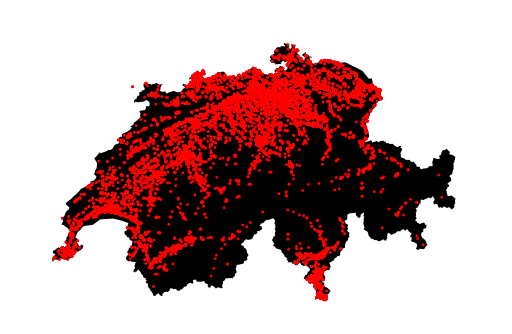

```mathematica
GeoGraphics[{{GeoStyling["ReliefMap"],Polygon[LinguisticAssistant]},Red,PointSize->.004,Point[GeoPosition[#]&/@immoDataSet[[1;;-1,{2,3}]]]},GeoBackground->None,GeoRange->{{45.8,47.9},{5.9,10.6}},ImageSize->512]
```

### Histograms

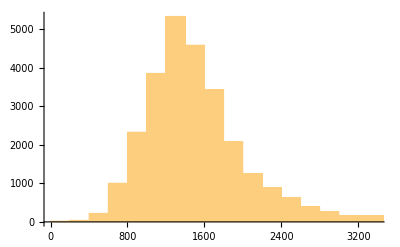

```mathematica
(*prices*)
Histogram@Cases[immoDataSet[[1;;-1,4]],_Integer,1]
```

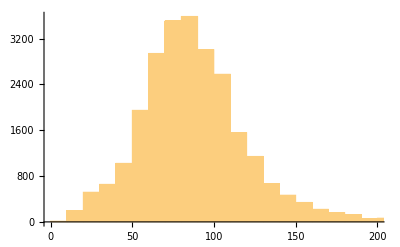

```mathematica
(*apartment size*)
Histogram@Cases[immoDataSet[[1;;-1,6]],_Integer,1]
```

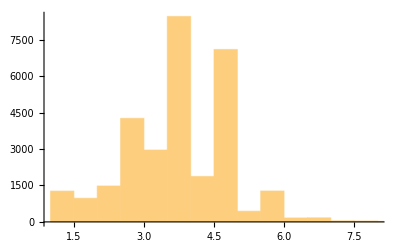

```mathematica
(*apartment rooms*)
Histogram@Cases[immoDataSet[[1;;-1,8]],_Integer|_Real,1]
```

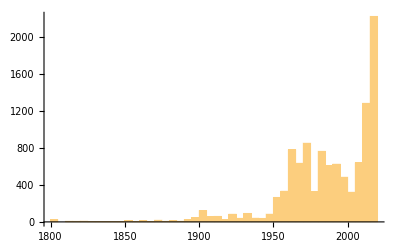

```mathematica
(*year of construction*)
Histogram[Cases[immoDataSet[[1;;-1,9]],_Integer,1],{1800,2020,5}]
```

### Correlation of price and area

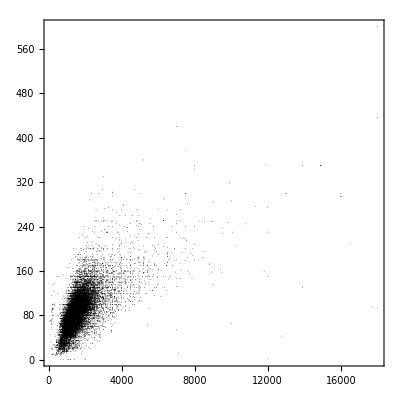

```mathematica
Graphics[{PointSize->.001,Point[Cases[immoDataSet[[1;;-1,{4,6}]],{_Integer,_Integer},1]]},Frame->True,AspectRatio->1]
```

### Correlation of location and price / area

```mathematica
vecs=Cases[immoDataSet[[1;;-1,{2,3,4,6}]],{a_Real,b_Real,c_Integer,d_Integer}:>{1. c/d,a,b},1];
```

```mathematica
vecs[[1;;-1,1]]
{q1,q2}=Quantile[vecs[[1;;-1,1]],{1/10,9/10}]
```

{54.4444,46.,94.2857,87.5,55.,32.0313,33.2857,67.1667,59.3333,21.8919,31.1765,25.3226,35.,36.3333,22687,11.8343,12.1649,8.79121,9.88889,10.4651,10.1345,13.4615,12.963,12.2642,13.2547,14.1604,14.0777,14.2857,12.5974}
 |  |  |  |

{13.0556,27.6}

```mathematica
vecs1=Transpose[ReplacePart[Transpose[vecs],1->({q1,q2}=Quantile[vecs[[1;;-1,1]],{1/10,9/10}];
Rescale[Replace[vecs[[1;;-1,1]],{a_Real/;a<q1:>q1,a_Real/;a>q2:>q2,a_Real:>a},1]])]];
```

```mathematica
vecs2=Replace[vecs1,{a_Real,b_Real,c_Real}:>{ColorData["Rainbow"]@a,Point[GeoPosition@{b,c}]},1];
```

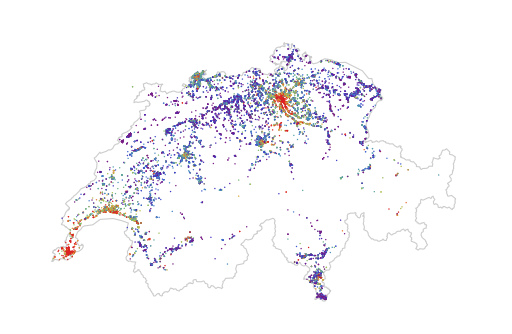

```mathematica
GeoGraphics[{{EdgeForm@Black,White,Polygon[LinguisticAssistant]},Red,PointSize->.002,vecs2},GeoBackground->None,GeoRange->{{45.8,47.9},{5.9,10.6}},ImageSize->512]
```

## Unsupervised : looking for friends

```mathematica
immoDataSet=Uncompress@Import[CloudObject@"https://www.wolframcloud.com/obj/hovestadt/homegate30KDSC.txt","Text"];
```

```mathematica
Length@immoDataSet
```

30572

```mathematica
fe1=FeatureExtraction@immoDataSet[[All,-1]]
```

FeatureExtractorFunction[…]

```mathematica
dr1=DimensionReduction[fe1@immoDataSet[[All,-1]],1]
```

DimensionReducerFunction[…]

```mathematica
pv1=Flatten@dr1@fe1@immoDataSet[[All,-1]]
```

{0.705558,-2.38018,-0.673358,-1.5956,3.2974,4.43662,-1.5956,0.155396,-0.415719,-4.81423,-0.673358,-0.0868064,30549,-1.18878,-0.0868064,-0.0868064,-0.600048,-0.0868064,-0.943052,-0.0868064,-4.54107,-0.0868064,-0.0868064,-0.0868064}
 |  |  |  |

```mathematica
fe2=FeatureExtraction@immoDataSet[[All,7]];
dr2=DimensionReduction[fe2@immoDataSet[[All,7]],1];
pv2=Flatten@dr2@fe2@immoDataSet[[All,7]]
```

{2.1869,-0.526842,-0.526849,-0.526847,2.1869,3.82102,-0.526851,-0.526847,-0.526847,3.82102,3.82103,-0.526845,30548,-0.526844,-0.526848,-0.52684,-0.526847,2.73582,-0.526847,-0.526842,-0.526844,-0.526843,-0.526848,-0.526846,-0.526844}
 |  |  |  |

```mathematica
vecs=Flatten/@Transpose[{immoDataSet[[All,{2,3,4,5,6,8,9}]],pv1,pv2}];
```

```mathematica
fe=FeatureExtraction@vecs;
pv=fe@vecs;
Graphics3D[{Point@DimensionReduce[pv,3]}]
```

-Graphics3D-

```mathematica
friends=Nearest[pv->"Index",fe@vecs[[1012]],12];
imgs=ImageResize[Import@First@StringCases[Import[immoDataSet[[#,1]],"Text"],Shortest["\"image\":\""~~a__~~"\""]:>a],128]&/@friends
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GeoGraphics[{Red,PointSize@.02,Point[GeoPosition[#[[1;;2]]]&/@vecs[[friends]]]},GeoBackground->"StreetMap"]
```

-Graphics-

## Supervised: predict the price of an apartment

```mathematica
immoDataSet=Uncompress@Import[CloudObject@"https://www.wolframcloud.com/obj/hovestadt/homegate30KDSC.txt","Text"];

fe1=FeatureExtraction@immoDataSet[[All,-1]];
dr1=DimensionReduction[fe1@immoDataSet[[All,-1]],1];
pv1=Flatten@dr1@fe1@immoDataSet[[All,-1]];

fe2=FeatureExtraction@immoDataSet[[All,7]];
dr2=DimensionReduction[fe2@immoDataSet[[All,7]],1];
pv2=Flatten@dr2@fe2@immoDataSet[[All,7]];
```

```mathematica
ds=Flatten/@Transpose[{immoDataSet[[All,{2,3,4,5,6,8,9}]],pv1,pv2}];
ds1=SynthesizeMissingValues[ds];
ds2=Cases[ds1,{a1_,a2_,a3_,a4_,a5_,a6_,a7_,a8_,a9_}:>{a1,a2,a4,a5,a6,a7,a8,a8}->a3,1];
```

```mathematica
trainingSet=RandomSample[ds1,28000];
testSet=Complement[ds1,trainingSet];
```

```mathematica
testSet1=Cases[testSet,(a_->b_Integer):>(a->b),1];
testSet2=Rule@@@Transpose[{SynthesizeMissingValues[testSet1[[All,1]]],testSet1[[All,2]]}];
```

SynthesizeMissingValues::mlmpty: The dataset should contain at least one example.

Transpose::nmtx: The first two levels of {SynthesizeMissingValues[{}],{}} cannot be transposed.

```mathematica
s
```

```mathematica
Length@testSet1
```

0

```mathematica
pricePredict=Predict[trainingSet]
```

Predict::bdfmt: Argument {{47.5706,7.57406,1675,243.735,56,2.5,1944.02,0.511694,-0.526844},{46.6189,7.06163,1390,320,96,4,1972,-1.98682,-0.526845},{47.5615,7.57148,1310,180,55,2.5,1962,-0.998454,-0.526844},«46»,{47.0834,7.40646,1307.58,247.526,100,3.5,1986.54,-0.0868064,-0.526845},«27950»} should be a rule or a list of rules.

Predict[{{47.5706,7.57406,1675,243.735,56,2.5,1944.02,0.511694,-0.526844},{46.6189,7.06163,1390,320,96,4,1972,-1.98682,-0.526845},27996,{46.1897,6.15754,1800,169.247,85.134,3,1982.93,4.73342,-0.526845},{46.2746,6.93918,1250,190,67,3.5,2015,-1.45363,-0.526848}}]
 |  |  |  |

```mathematica
PaneSelectorBox[]
```

PaneSelectorBox[]